# Lab 6: FT Audio Processing

Each case in each exercise below requires you to use an audio signal.  I provide three alternatives for obtaining an audio signal.  I encourage you to try all three before you really get started.

For both of the two exercises below, keep careful notes of what you try and what you observe.  Write a one-page single-spaced report on your results.  Submit only the report.  You don’t need to submit the Mathematica notebook unless you type the report in the Mathematica notebook.  If you do submit the notebook, please delete the audio clips first in order to reduce the file size.

(1) Record a variety of different sounds, compute their frequency spectra, and describe what you observed.  I won’t dictate what you should try.  But I can make the following suggestions.  Consider that a very quick time pulse (such as a loud clap) has a very broad frequency response, whereas a pure computer-generated note has a very sharp frequency response; this is the uncertainty principle at work.  Also consider that each musical instrument has a characteristic set of harmonic amplitudes; you could compare the same musical note played on different instruments or sung by very different human voices.   You do NOT need the filter section below for this first exercise.

(2)  Record or obtain at least two different audio signals.  Then apply at least 3 interesting filter configurations to each one.  This means that for each example, you compute the frequency spectrum, filter it, transform back to time space (to the filtered audio signal), and both visualize and listen to the result.  For a given audio clip, you might need need to try more than 3 filter configurations to find 3 interesting results worth reporting on. What would be interesting?  That’s up to you.  If filter out the high frequencies, or the low frequencies, or some other key range of frequencies from the spectrum, the resulting filtered audio signal should sound predictably different.  The axelf2.wav example that I have provided is nice because it includes both high and low-frequency sounds.

### Audio alternative #1: Import an audio file (possibly one that you recorded yourself).

Import an audio clip into Mathematica.  You could choose to record a few seconds own voice or a musical instrument.  Or you could use an audio clip that you already have on hand.  I provided one nice clip (axelf2.wav) in the Class Notes section of the course website.  Either way, the format needs to be one that Mathematica supports (https://reference.wolfram.com/language/guide/AudioFormats.html).  Place the audio file and this Mathematica notebook in the same folder.  There are many phone and computer apps for recording and saving audio clips, some of which can export to WAV files (a format that Mathematica supports).  On my Windows laptop, I used the command “soundrecorder /file myvoice.wav” in the Run window to specify the WAV format for this built-in app.

```mathematica
SetDirectory[NotebookDirectory[]]
myaudio=Import["Lab6M-axelf2.wav"];
myaudio=AudioChannelMix[myaudio,"Mono"]
```

```mathematica
(* If the audio clip is so long that later steps run slow on your computer, trim it to 5 seconds, or whatever works for you. *)
myaudio = AudioTrim[myaudio,{0,5.0}]
```

### Audio alternative #2: Record roughly 5 seconds of audio directly within Mathematica.

You’ll need a microphone of some kind to do this.  Your computer may or may not have a built in microphone (e.g. for video chat).  Press Record (red circle), Pause (blue vertical bars), and finally exit (gray square), to create the audio object.  Then play it back to verify that it worked.  You can modify the prefactor of 1.0 to change the volume of the clip.

```mathematica
myaudio=1*AudioCapture[]
```

### Audio alternative #3: Generate an audio signal from a function.

Choose one of the following functions, or make your own.

```mathematica
myaudio=Sound[Play[Sin[2 Pi *500t],{t,0,2}]]
```

-Graphics-

```mathematica
myaudio=Sound[Play[Sin[500t (1+t^3)],{t,0,2.9}]]
```

```mathematica
myaudio=Sound[ListPlay[RandomReal[{-1,1},20000]]]
```

### (1) Calculate signal characteristics. Visualize signal in time chunks. Repeat when myaudio changes.

```mathematica
rate= myaudio//AudioSampleRate//QuantityMagnitude; (* samplerate in Hz *)
duration = myaudio//Duration//QuantityMagnitude ;(* duration in seconds *)
ampdata = myaudio//AudioData;
ampdata =  If[Length[Dimensions[ampdata]]>1,ampdata[[1]],ampdata];
samplenum =ampdata//Length; (* number of samples *)

timerange = duration; (* maximum time in seconds *)
timestep = duration/samplenum//N; (* time step in seconds *)
freqrange = rate/2//N; (* maximum frequency in Hz *)
freqstep=freqrange/samplenum//N; (* frequency step in Hz *)

Print["rate = ", rate, ", samplenum = ", samplenum, ", timestep = ", timestep, ", timerange = ", timerange, ", freqstep = ", freqstep, ", freqrange = ", freqrange]

chunksize =Min[1000,samplenum/50];
chunkcount = Min[Floor[samplenum/chunksize],50];
Print["chunksize = ",chunksize,", chunkcount = ",chunkcount];
ListAnimate[Table[ListPlot[ampdata[[(n-1)*chunksize+1;;n*chunksize]],Joined->True,Frame->True,PlotRange->All],{n,1,chunkcount}]]
```

rate = 44100, samplenum = 264600, timestep = 0.0000226757, timerange = 6., freqstep = 0.0833333, freqrange = 22050.

chunksize = 1000, chunkcount = 50

### (2) Compute and visualize the frequency spectrum

Use the FourierDCT function to compute a frequency spectrum.  Then zoom in on the interesting region of the spectrum when you plot it.  The goodrange function that I prepared might help you to identify the interesting range (everything below the point where the signal more or less dies away).  But you can just as easily bypass (overwrite) this function to choose the maximum interesting frequency (freqmax) by eye if you prefer by redefining it on the next line.

```mathematica
rawspectrum = FourierDCT[ampdata]; (* raw discrete Fourier transform *)
ListPlot[rawspectrum,Joined->True,Frame->True,DataRange->{0,freqrange},PlotRange->All,AspectRatio->1/6]

goodrange[rawspectraldata_,threshold_] := Module[{len,absdata,maxabs,blocksize,blockmaxvals,maxresiduals,threshhold,maxlargenough,falsepositions,cutoff},
len = rawspectraldata//Length;
absdata = rawspectraldata//Abs;
maxabs=absdata//Abs//Max;
blocksize =Min[Ceiling[len/10000],100];
blockmaxvals =Max/@Partition[absdata,blocksize];
maxresiduals = Table[blockmaxvals[[i;;]]//Max,{i,Length[blockmaxvals]}];
maxlargenough=(#>maxabs*threshold)&/@maxresiduals;
falsepositions = Position[maxlargenough,False];
cutoff = If[Length[falsepositions]>0,Min[1.1*falsepositions[[1,1]]*blocksize//Ceiling,samplenum],samplenum];
cutoff*freqstep
]
freqmax = goodrange[rawspectrum,0.05]

(* Plot the abs value of the spectrum. If you don't like the freqmax value obtained above, set it to whatever you prefer. *)
ListPlot[rawspectrum//Abs,Joined->True,Frame->True,DataRange->{0,freqrange},PlotRange->{{1,freqmax},All}]
```

-Graphics-

4492.17

-Graphics-

### (3) Modify the frequency spectrum with a filter

A frequency filter suppresses some regions of the spectrum while leaving other regions untouched.  The filter is a function of k that multiplies the amplitude associated with a given k vector by some number between 0 and 1.  If you actually want to enhance rather than suppressing a particular region, just multiply the whole spectrum by a number larger than 1, and then apply a filter that suppresses other regions.

I’ve constructed a few filters that you can try (see below).  In each filter, feel free to modify the coefficients in front of freqmax or to simply replace instances of freqmax with numerical frequencies.  Try building your own filters if you want to.  Have fun!

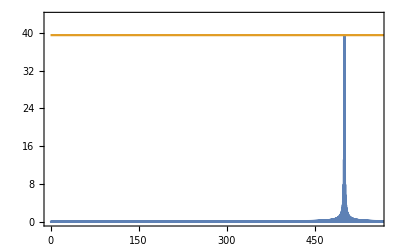

```mathematica
(* possible filter functions *)
filternone[findex_]:= 1
filterlinearpositive[findex_]:= findex*freqstep/(1.0freqmax)
filterparabolic[findex_]:=(findex*freqstep/(0.5freqmax))^2
filterlinearnegative[findex_] := 1-findex*freqstep/(0.5freqmax)
filtergaussian[findex_]:=Exp[-0.5((findex*freqstep-0.5freqmax)/(0.125freqmax))^2]
filterbox[findex_] := If[0.25*freqmax<findex*freqstep<0.75freqmax,1,0]
filterantibox[findex_] := If[0.25*freqmax<findex*freqstep<0.75freqmax,0,1]

(* Choose which filter to use. *)
filteractual = filternone;
(* Build filter so as to stay between 0 and 1. *)
filterlist=Table[Max[Min[filteractual[i],1],0],{i,samplenum}]//Chop;

(* Filter the spectrum *)
filteredspectrum =filterlist*rawspectrum;

(* Plot the filtered spectrum and the filter function.  The plot rendering may be slow for large samplenum.*)
maxfabs = rawspectrum//Abs//Max;
ListPlot[{filteredspectrum//Abs,maxfabs*filterlist},Joined->True,Frame->True,DataRange->{0,freqrange},PlotRange->{{0,freqmax},{0,1.1maxfabs}}]
```

### (4) Calculate, visualize, and listen to the filtered audio signal

For each audio signal and filter configuration that you attempt, use the cells below to visualize and play back the filtered audio signal.

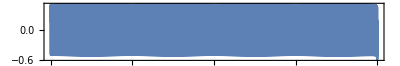

-Graphics-

```mathematica
filteredampdata= FourierDCT[filteredspectrum];

ListPlot[filteredampdata,DataRange->{0,timerange},Joined->True,Frame->True,PlotRange->All,AspectRatio->1/6]

filteredaudio = ListPlay[filteredampdata,SampleRate->rate]
```